#### Meta-population reproduction numbers:

```mathematica
(*SetDirectory["C:\\Users\\zfeng\\OneDrive - National Science Foundation\\ZF\\1IRD\\Glasser\\MS24\\Ludmil\\H_matrix\\"] *)
SetDirectory["/home/ltz1/github/ludmil02/Working_dirs/MathBio/nb_Data"]
```

SetDirectory::cdir: Cannot set current directory to /home/ltz1/github/ludmil02/Working_dirs/MathBio/nb_Data.

$Failed

```mathematica
m=4; n=4; 
 x=7;k=1/5x; ξ=1/2 x; 
γa=1/7;γs=1/5;γm=1/5;γh=1/10 ; (* age dependent? *)
ω=x 1/(1×182.5);ωv=x 1/(1×182.5);bS=0.31;bI=0.31;ϵ1=0.8;ϵ2=0.8; ϵ3=0.8; 
vγa=Table[γa,{j,n}]x;
vγs=Table[γs,{j,n}]x; 
vγm=Table[γm,{j,n}]x; 
vγh=Table[γh,{j,n}]x; 
vβ=25*{0.0794498883424254,0.07378658226273424,0.08093055958811815,0.21470494228237624};
vp={0.9706574350846233,0.8938517556772458,0.6548278086229462,0.28889590656079006};
vq={0.9853287175423117,0.9469258778386229,0.8274139043114731,0.6444479532803951};
vδs={0.0005227159753841133,0.010632200553688746,0.02953817543239884,0.057703228431405976};
vδm={0.00026135798769205665,0.005316100276844373,0.01476908771619942,0.028851614215702988};
mN={{12861646,14862307,14294150,13831766},{17039947,18046593,16847952,16382252},{31775045,34108261,31760738,29018710},{19577717,22475544,19374280,17227215}};
ma={{17.073281356320802,17.011021886542494,14.464215476578978,3.6569593567943652},{13.676777723325813,13.626903952047815,11.586751010942738,2.929455634349783},{15.06551341188455,15.010575473629661,12.763266047514328,3.2269116338380703},{13.603540223639197,13.553933520407654,11.524705352915733,2.913768751778259}};
```

```mathematica
mc={{{{0.20197824889699842,0.059415283664697484,0.04892172067444938,0.008030707230540838},{0.1521469690453322,0.044793777860070695,0.03339288184769395,0.002877214165782988},{0.16553227488415234,0.04874272018491846,0.03561633471701904,0.0026950721853331765},{0.13265108985915125,0.03912354820446772,0.023571691514938764,0.0005104650644532836}},{{0.06103198838432115,0.1621666401078013,0.08879328829009539,0.012414165389758761},{0.0459744160482341,0.12225905533493119,0.06060832987601685,0.004447704478623026},{0.050019068553821766,0.13303720313296225,0.06464391343488654,0.004166142642932759},{0.04008332491079227,0.10678286747259674,0.04278279609376618,0.0007890958484599316}},{{0.061021070464599016,0.1080249810376071,0.14362458579558354,0.02178381591253095},{0.04596619175476153,0.08144111591294141,0.09803495784237114,0.00780463064199165},{0.05001012071860447,0.08862082445675072,0.10456257978596326,0.007310558668234078},{0.04007615446566739,0.07113187537338422,0.06920186746625413,0.0013846697027553945}},{{0.0530544005552305,0.07868141298325652,0.11156873991077054,0.14315896066513709},{0.039965027338719886,0.05931870585316376,0.0761543481785637,0.05129050004687597},{0.043480996911706815,0.0645481408191205,0.0812250577010754,0.048043556052264826},{0.03484397005077645,0.05180983517672048,0.05375657036651684,0.009099777390100771}}},{{{0.1864572151389774,0.05489509996649521,0.04092321913380201,0.003526046848494684},{0.15883787710504257,0.04672482099647865,0.038472569688521994,0.006315434929836045},{0.16645777750802396,0.048999330689790524,0.037222141625251635,0.0036235420810433495},{0.1384701016999805,0.04080592480578916,0.02714997342339332,0.0011189243590791157}},{{0.05620517348314829,0.14946555074840534,0.074095594637493,0.005437458989376001},{0.04787967272668808,0.12721993598921966,0.06965844790907054,0.00973892858108688},{0.05017659550199961,0.13341285383071985,0.06739442242768076,0.0055878047877789255},{0.0417400639737951,0.11110427030131684,0.049157751217494744,0.001725474894726343}},{{0.05598955512300673,0.09920012240767083,0.11941240869771409,0.009506504255907459},{0.04769599325596215,0.08443573224488508,0.11226150612140896,0.01702691757031642},{0.049984104409647206,0.08854596503673143,0.10861280423287652,0.009769359198844548},{0.04157993771515215,0.07373978257008608,0.07922259761545583,0.0030167095443343977}},{{0.0483897647994067,0.07182325186748455,0.09220789380625656,0.06210267824107499},{0.041221936671215216,0.0611334816575884,0.08668610865372699,0.11123091673257021},{0.04319946909344056,0.06410938811695327,0.08386865341655675,0.06381981794941248},{0.035936049178990924,0.053389359283444786,0.06117411873395686,0.019707111797920892}}},{{{0.18556130844105437,0.05464047987511577,0.03992583124100672,0.0030211698679518018},{0.1522624964435324,0.04482073788669957,0.034047890652404864,0.003314531597667506},{0.1762963105157434,0.05186051149336481,0.04270122602847936,0.007009586741681536},{0.1370960269820946,0.04041057478883919,0.02613515273683758,0.0008961647075264086}},{{0.05599820943381795,0.14894010182362313,0.07237126775468089,0.004664151792412439},{0.04594938048450658,0.12217325469894243,0.06171666147695607,0.005117050403640263},{0.053202242437334624,0.1413624089704349,0.07740206694021748,0.010821561843342861},{0.041372482744302365,0.11015194481375509,0.04737369461664491,0.001383519765388032}},{{0.055880628953818706,0.09902370436004378,0.11683680502094429,0.008168718861595085},{0.045852899717216664,0.0812276083196121,0.09963591584396908,0.008961918052484497},{0.05309053270114724,0.09398563061336453,0.12495857104461666,0.018952705717133245},{0.04128561217417128,0.07323516960420862,0.07648050521663968,0.002423073799034595}},{{0.04852266901536028,0.07203257273247518,0.09064319750041606,0.05361426218857699},{0.03981531915490311,0.05908720181678404,0.07729857039792182,0.058820315929519154},{0.046099952601390444,0.06836773898448949,0.09694414728763369,0.12439347598050467},{0.03584941923755752,0.053273281535798744,0.05933436418464847,0.01590351145202035}}},{{{0.17692165561991846,0.05218052056270084,0.03143843516862934,0.0006808261012789027},{0.15069897386425823,0.044409666204609816,0.029547700804121193,0.001217741235651662},{0.163113647303639,0.04807955699770153,0.031094993630267853,0.0010662358147586787},{0.1710191212768521,0.05030813792198626,0.04142302315613488,0.0067997643374913255}},{{0.05402593029206072,0.1439262777551564,0.057664386988987765,0.0010635753744862712},{0.046018404183184,0.12249241449207234,0.05419640146414941,0.0019023353956358151},{0.049809428405089215,0.1326148455433863,0.057034446418792614,0.001665656110778397},{0.05222349458769408,0.13876180141215785,0.07597812119836828,0.010622480378000503}},{{0.054942625759409065,0.0975186382104811,0.0948726831888986,0.0018983205922129109},{0.04679923039573194,0.08299591734527946,0.08916695892507336,0.0033953799057967727},{0.050654579557569544,0.08985446817352293,0.09383626963688473,0.002972943310353709},{0.05310960687708606,0.09401939743322546,0.12500346571129078,0.018959514977183435}},{{0.05103757114600094,0.07588825685021303,0.07873972973366654,0.01332886394068318},{0.04347296871757569,0.06458678677837276,0.07400425508103237,0.02384031284122476},{0.04705429841233032,0.06992405846740708,0.07787955670772401,0.020874217479185664},{0.0493348343305421,0.07316517449633562,0.10374681915848274,0.13312229585922322}}}};
```

```mathematica
(* At t0=348 for vψS[t], vS[t], and ψI. *)
vψS={0.7781979107138681,0.7798533321459905,0.7865615336962511,0.7801996496586996};
vS={0.35861308333097464,0.4312100933817163,0.4612003634870343,0.3916131469870049};
vψI=ψI={0.7781979107138681,0.7798533321459905,0.7865615336962511,0.7801996496586996};

(* At t0=725 for vψS[t], vS[t], and ψI. 

ψI={0.8225583285710945,0.8238826657167924,0.8292492269570009,0.8241597197269597};
vψS={0.8225583285710945,0.8238826657167924,0.8292492269570009,0.8241597197269597};
vS={0.7024221010188523,0.7349559739895175,0.717797338653636,0.6535707127743224};   *)
```

```mathematica
mχ1={{χ111,χ112,χ113,χ114},{χ121,χ122,χ123,χ124},{χ131,χ132,χ133,χ134},{χ141,χ142,χ143,χ144}}={{0.25,0.50,0.16,0.12},{0.14,0.27,0.095,0.07},{0.17,0.35,0.12,0.09},{0.16,0.31,0.11,0.08}};
mχ2={{χ211,χ212,χ213,χ214},{χ221,χ222,χ223,χ224},{χ231,χ232,χ233,χ234},{χ241,χ242,χ243,χ244}}={{0.002,0.007,0.0006,0.0003},{0.003,0.012,0.001,0.0007},{0.006,0.024,0.002,0.001},{0.015,0.054,0.005,0.003}};
mχ3={{χ311,χ312,χ313,χ314},{χ321,χ322,χ323,χ324},{χ331,χ332,χ333,χ334},{χ341,χ342,χ343,χ344}}={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
```

```mathematica
Ωmat=Table[0,{i,1,m}];
ψImat=Table[0,{i,1,m}];
ccMat=Table[0,{i,1,m},{p,1,m}];
```

```mathematica
NPII=Table[1,{i,1,m},{j,1,n}];
```

```mathematica
Table[ψImat[[i]]=DiagonalMatrix[Flatten[{Table[NPII[[i,j]],{j,1,n}],Table[NPII[[i,j]],{j,1,n}]}]],{i,1,m}]
```

{{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}}

```mathematica
ccM=Partition[Flatten[Table[mc[[i,j,p,q]],{i,1,m},{j,1,n},{p,1,m},{q,1,n}]],m×n]//Quiet;
```

```mathematica
Dimensions[ccM]
```

{16,16}

```mathematica
(* Using the mixing matrix cM to add double rows. There are m^2 block matrices each 2n by 2n *)
Table[ccMat[[i,p]]=Flatten[Table[{Flatten[Table[{ccM[[(i-1) n+k,n (p-1)+r]],ccM[[(i-1) n+k,n (p-1)+r]]},{r,1,n}]],Flatten[Table[{ccM[[(i-1) n+k,n (p-1)+r]],ccM[[(i-1) n+k,n (p-1)+r]]},{r,1,n}]]},{k,1,n}],1],{i,1,m},{p,1,m}] ;
Dimensions[ccMat]
```

{4,4,8,8}

```mathematica
sdfe=Table[mN[[i,j]]×(1+mχ1[[i,j]]/(ωv+ϵ2 mχ2⟦i,j⟧)(1+(ϵ2 mχ2⟦i,j⟧)/ω+(ϵ2 mχ2⟦i,j⟧)/ω×(1+(ϵ3 mχ3⟦i,j⟧)/ω)))^(-1),{i,1,m},{j,1,n}]
vdfe=Table[mχ1[[i,j]]/(ωv+ϵ2 mχ2⟦i,j⟧)×sdfe[[i,j]],{i,1,m},{j,1,n}]
pdfe=Table[(ϵ2 mχ2⟦i,j⟧)/ω×vdfe⟦i,j⟧,{i,1,m},{j,1,n}]
```

{{1.65341×10^6,946857.,2.73678×10^6,3.33454×10^6},{3.5026×10^6,1.91001×10^6,4.77632×10^6,5.74562×10^6},{5.36278×10^6,2.59005×10^6,7.46635×10^6,8.54907×10^6},{3.17537×10^6,1.6819×10^6,4.68126×10^6,5.36918×10^6}}

{{1.03452×10^7,1.07705×10^7,1.12752×10^7,1.03675×10^7},{1.20317×10^7,1.07536×10^7,1.15882×10^7,1.03349×10^7},{2.1125×10^7,1.57501×10^7,2.24236×10^7,1.965×10^7},{1.00893×10^7,6.39299×10^6,1.21573×10^7,1.05391×10^7}}

{{431541.,1.57249×10^6,141101.,64870.8},{752839.,2.69148×10^6,241697.,150889.},{2.64364×10^6,7.88405×10^6,935385.,409842.},{3.15651×10^6,7.20033×10^6,1.26784×10^6,659449.}}

```mathematica
MatrixForm[{{1.2861646*^7,1.4862307*^7,1.429415*^7,1.3831766*^7},{1.7039947*^7,1.8046593*^7,1.6847952*^7,1.6382252*^7},{3.1775045*^7,3.4108261*^7,3.1760738*^7,2.901871*^7},{1.9577717*^7,2.2475544*^7,1.937428*^7,1.7227215*^7}}]
```

(1.28616×10^7 | 1.48623×10^7 | 1.42942×10^7 | 1.38318×10^7
1.70399×10^7 | 1.80466×10^7 | 1.6848×10^7 | 1.63823×10^7
3.1775×10^7 | 3.41083×10^7 | 3.17607×10^7 | 2.90187×10^7
1.95777×10^7 | 2.24755×10^7 | 1.93743×10^7 | 1.72272×10^7)

```mathematica
Y=Table[vψS[[j]]×vS[[i]]×ma[[i,j]]×vβ[[j]]×(sdfe[[i,j]]/mN[[i,j]]),{i,1,m},{j,1,n}]
Z=Table[vψS[[j]]×vS[[i]]×ma[[i,j]]×vβ[[j]]×((1-ϵ1)×vdfe[[i,j]]+pdfe[[i,j]])/mN[[i,j]],{i,1,m},{j,1,n}]
```

{{1.21661,0.559094,1.58047,1.32401},{1.87378,0.894658,2.25415,1.85535},{1.8126,0.756249,2.20219,1.83614},{1.33556,0.571402,1.73544,1.48934}}

{{1.83996,2.20045,1.38376,0.849061},{1.69006,2.26811,1.20786,0.716183},{2.32157,3.22176,1.59865,0.932093},{2.17635,2.8806,1.37141,0.767604}}

```mathematica
Table[Ωmat[[i]]=DiagonalMatrix[Flatten[Table[{Y[[i,j]],Z[[i,j]]},{j,1,n}]]],{i,1,m}]//Quiet;
```

```mathematica
(*NPII=Table[vψI[t][[j]],{j,1,n}]//Quiet;*)
```

```mathematica
(*Table[ψImat[[i]]=DiagonalMatrix[Flatten[{Table[{NPII[[j]],NPII[[j]]},{j,1,n}]}]],{i,1,m}];  *)
```

```mathematica
vη={ηa,ηps,ηpm,ηs,ηm,ηh}={0.5,1.25,1,1,0.75,0.1}; (*Notice the order of vη *)
η={ηa,ηps,ηpm, ηs,ηm,ηh}; 
Pas=Table[vp[[j]],{j,1,n}]; 
Pps=Table[1-vp[[j]],{j,1,n}]; 
Ps=Table[1-vp[[j]],{j,1,n}]; 
Phs=Table[vδs[[j]]/(vγs[[j]]+vδs[[j]]),{j,1,n}]; 

Pam=Table[vq[[j]],{j,1,n}]; ;
Ppm=Table[1-vq[[j]],{j,1,n}]; 
Pm=Table[1-vq[[j]],{j,1,n}]; 
Phm=Table[vδm[[j]]/(vγm[[j]]+vδm[[j]]),{j,1,n}]; 

Ta=Table[1/vγa[[j]],{j,1,n}];
Tp=1/ξ;
Ts=Table[1/(vγs[[j]]+vδs[[j]]),{j,1,n}];
Tm=Table[1/(vγm[[j]]+vδm[[j]]),{j,1,n}];
Th=Table[1/(vγh[[j]]),{j,1,n}];
Q0=Table[ηa×Pas[[j]]×Ta[[j]]+ηps×Pps[[j]]×Tp+ηs×Ps[[j]]×Ts[[j]],{j,1,n}];
Q=DiagonalMatrix[Flatten[Table[{Q0[[j]],Q0[[j]]},{j,1,n}]]]//Quiet;
```

```mathematica
Q0
Q
```

{0.516759,0.560085,0.692147,0.886239}

{{0.516759,0.,0.,0.,0.,0.,0.,0.},{0.,0.516759,0.,0.,0.,0.,0.,0.},{0.,0.,0.560085,0.,0.,0.,0.,0.},{0.,0.,0.,0.560085,0.,0.,0.,0.},{0.,0.,0.,0.,0.692147,0.,0.,0.},{0.,0.,0.,0.,0.,0.692147,0.,0.},{0.,0.,0.,0.,0.,0.,0.886239,0.},{0.,0.,0.,0.,0.,0.,0.,0.886239}}

```mathematica
(* Create tables of matrices for the (i,p) block H_{i,p}. Each block has dimension n by n and there are m blocks based on m locations: *)
mH=Table[0,{i,1,m},{p,1,m}];
```

```mathematica
Dimensions[Ωmat]
Dimensions[ccMat]
Dimensions[ψImat]
Dimensions[Q]
```

{4,8,8}

{4,4,8,8}

{4,8,8}

{8,8}

```mathematica
(* Using the block matrices to calculate H_{ip}: *)
Table[mH[[i,p]]=Dot[Ωmat[[i]],ccMat[[i,p]],ψImat[[p]],Q],{i,1,m},{p,1,m}];
```

```mathematica
L1=Partition[Flatten[Transpose[Table[mH[[1,p]],{p,1,m}]]],m×2n];
L2=Partition[Flatten[Transpose[Table[mH[[2,p]],{p,1,m}]]],m×2n];
L3=Partition[Flatten[Transpose[Table[mH[[3,p]],{p,1,m}]]],m×2n];
L4=Partition[Flatten[Transpose[Table[mH[[4,p]],{p,1,m}]]],m×2n];
```

```mathematica
Dimensions[L1]
```

{8,32}

```mathematica
NGM=Join[L1,L2,L3,L4];
```

```mathematica
Export["NGM.csv",NGM];
```

```mathematica
Dimensions[NGM]
```

{32,32}

```mathematica
Re[Eigenvalues[NGM,1]]
```

{1.98388}

```mathematica
Abs[Eigenvectors[NGM,1]]
```

{{0.115796,0.175127,0.0570921,0.224699,0.169168,0.148112,0.144417,0.0926113,0.179502,0.161902,0.0920816,0.233443,0.243629,0.130546,0.206953,0.0798859,0.174253,0.223183,0.0781709,0.333023,0.239205,0.173648,0.206972,0.105067,0.127014,0.206974,0.0582646,0.293729,0.184917,0.146128,0.160343,0.0826406}}

```mathematica
Abs[Eigenvectors[Transpose[NGM],1]]
```

{{0.217614,0.217614,0.246504,0.246504,0.233572,0.233572,0.0346896,0.0346896,0.177641,0.177641,0.201194,0.201194,0.195456,0.195456,0.0310681,0.0310681,0.19504,0.19504,0.220958,0.220958,0.213857,0.213857,0.0345837,0.0345837,0.166244,0.166244,0.188497,0.188497,0.166272,0.166272,0.0175688,0.0175688}}

## Matrices involved in H (not including Ωmat): ccMat, ψImat, and Q

```mathematica
ccMat
```

{{{{0.201978,0.201978,0.0594153,0.0594153,0.0489217,0.0489217,0.00803071,0.00803071},{0.201978,0.201978,0.0594153,0.0594153,0.0489217,0.0489217,0.00803071,0.00803071},{0.061032,0.061032,0.162167,0.162167,0.0887933,0.0887933,0.0124142,0.0124142},{0.061032,0.061032,0.162167,0.162167,0.0887933,0.0887933,0.0124142,0.0124142},{0.0610211,0.0610211,0.108025,0.108025,0.143625,0.143625,0.0217838,0.0217838},{0.0610211,0.0610211,0.108025,0.108025,0.143625,0.143625,0.0217838,0.0217838},{0.0530544,0.0530544,0.0786814,0.0786814,0.111569,0.111569,0.143159,0.143159},{0.0530544,0.0530544,0.0786814,0.0786814,0.111569,0.111569,0.143159,0.143159}},{{0.152147,0.152147,0.0447938,0.0447938,0.0333929,0.0333929,0.00287721,0.00287721},{0.152147,0.152147,0.0447938,0.0447938,0.0333929,0.0333929,0.00287721,0.00287721},{0.0459744,0.0459744,0.122259,0.122259,0.0606083,0.0606083,0.0044477,0.0044477},{0.0459744,0.0459744,0.122259,0.122259,0.0606083,0.0606083,0.0044477,0.0044477},{0.0459662,0.0459662,0.0814411,0.0814411,0.098035,0.098035,0.00780463,0.00780463},{0.0459662,0.0459662,0.0814411,0.0814411,0.098035,0.098035,0.00780463,0.00780463},{0.039965,0.039965,0.0593187,0.0593187,0.0761543,0.0761543,0.0512905,0.0512905},{0.039965,0.039965,0.0593187,0.0593187,0.0761543,0.0761543,0.0512905,0.0512905}},{{0.165532,0.165532,0.0487427,0.0487427,0.0356163,0.0356163,0.00269507,0.00269507},{0.165532,0.165532,0.0487427,0.0487427,0.0356163,0.0356163,0.00269507,0.00269507},{0.0500191,0.0500191,0.133037,0.133037,0.0646439,0.0646439,0.00416614,0.00416614},{0.0500191,0.0500191,0.133037,0.133037,0.0646439,0.0646439,0.00416614,0.00416614},{0.0500101,0.0500101,0.0886208,0.0886208,0.104563,0.104563,0.00731056,0.00731056},{0.0500101,0.0500101,0.0886208,0.0886208,0.104563,0.104563,0.00731056,0.00731056},{0.043481,0.043481,0.0645481,0.0645481,0.0812251,0.0812251,0.0480436,0.0480436},{0.043481,0.043481,0.0645481,0.0645481,0.0812251,0.0812251,0.0480436,0.0480436}},{{0.132651,0.132651,0.0391235,0.0391235,0.0235717,0.0235717,0.000510465,0.000510465},{0.132651,0.132651,0.0391235,0.0391235,0.0235717,0.0235717,0.000510465,0.000510465},{0.0400833,0.0400833,0.106783,0.106783,0.0427828,0.0427828,0.000789096,0.000789096},{0.0400833,0.0400833,0.106783,0.106783,0.0427828,0.0427828,0.000789096,0.000789096},{0.0400762,0.0400762,0.0711319,0.0711319,0.0692019,0.0692019,0.00138467,0.00138467},{0.0400762,0.0400762,0.0711319,0.0711319,0.0692019,0.0692019,0.00138467,0.00138467},{0.034844,0.034844,0.0518098,0.0518098,0.0537566,0.0537566,0.00909978,0.00909978},{0.034844,0.034844,0.0518098,0.0518098,0.0537566,0.0537566,0.00909978,0.00909978}}},{{{0.186457,0.186457,0.0548951,0.0548951,0.0409232,0.0409232,0.00352605,0.00352605},{0.186457,0.186457,0.0548951,0.0548951,0.0409232,0.0409232,0.00352605,0.00352605},{0.0562052,0.0562052,0.149466,0.149466,0.0740956,0.0740956,0.00543746,0.00543746},{0.0562052,0.0562052,0.149466,0.149466,0.0740956,0.0740956,0.00543746,0.00543746},{0.0559896,0.0559896,0.0992001,0.0992001,0.119412,0.119412,0.0095065,0.0095065},{0.0559896,0.0559896,0.0992001,0.0992001,0.119412,0.119412,0.0095065,0.0095065},{0.0483898,0.0483898,0.0718233,0.0718233,0.0922079,0.0922079,0.0621027,0.0621027},{0.0483898,0.0483898,0.0718233,0.0718233,0.0922079,0.0922079,0.0621027,0.0621027}},{{0.158838,0.158838,0.0467248,0.0467248,0.0384726,0.0384726,0.00631543,0.00631543},{0.158838,0.158838,0.0467248,0.0467248,0.0384726,0.0384726,0.00631543,0.00631543},{0.0478797,0.0478797,0.12722,0.12722,0.0696584,0.0696584,0.00973893,0.00973893},{0.0478797,0.0478797,0.12722,0.12722,0.0696584,0.0696584,0.00973893,0.00973893},{0.047696,0.047696,0.0844357,0.0844357,0.112262,0.112262,0.0170269,0.0170269},{0.047696,0.047696,0.0844357,0.0844357,0.112262,0.112262,0.0170269,0.0170269},{0.0412219,0.0412219,0.0611335,0.0611335,0.0866861,0.0866861,0.111231,0.111231},{0.0412219,0.0412219,0.0611335,0.0611335,0.0866861,0.0866861,0.111231,0.111231}},{{0.166458,0.166458,0.0489993,0.0489993,0.0372221,0.0372221,0.00362354,0.00362354},{0.166458,0.166458,0.0489993,0.0489993,0.0372221,0.0372221,0.00362354,0.00362354},{0.0501766,0.0501766,0.133413,0.133413,0.0673944,0.0673944,0.0055878,0.0055878},{0.0501766,0.0501766,0.133413,0.133413,0.0673944,0.0673944,0.0055878,0.0055878},{0.0499841,0.0499841,0.088546,0.088546,0.108613,0.108613,0.00976936,0.00976936},{0.0499841,0.0499841,0.088546,0.088546,0.108613,0.108613,0.00976936,0.00976936},{0.0431995,0.0431995,0.0641094,0.0641094,0.0838687,0.0838687,0.0638198,0.0638198},{0.0431995,0.0431995,0.0641094,0.0641094,0.0838687,0.0838687,0.0638198,0.0638198}},{{0.13847,0.13847,0.0408059,0.0408059,0.02715,0.02715,0.00111892,0.00111892},{0.13847,0.13847,0.0408059,0.0408059,0.02715,0.02715,0.00111892,0.00111892},{0.0417401,0.0417401,0.111104,0.111104,0.0491578,0.0491578,0.00172547,0.00172547},{0.0417401,0.0417401,0.111104,0.111104,0.0491578,0.0491578,0.00172547,0.00172547},{0.0415799,0.0415799,0.0737398,0.0737398,0.0792226,0.0792226,0.00301671,0.00301671},{0.0415799,0.0415799,0.0737398,0.0737398,0.0792226,0.0792226,0.00301671,0.00301671},{0.035936,0.035936,0.0533894,0.0533894,0.0611741,0.0611741,0.0197071,0.0197071},{0.035936,0.035936,0.0533894,0.0533894,0.0611741,0.0611741,0.0197071,0.0197071}}},{{{0.185561,0.185561,0.0546405,0.0546405,0.0399258,0.0399258,0.00302117,0.00302117},{0.185561,0.185561,0.0546405,0.0546405,0.0399258,0.0399258,0.00302117,0.00302117},{0.0559982,0.0559982,0.14894,0.14894,0.0723713,0.0723713,0.00466415,0.00466415},{0.0559982,0.0559982,0.14894,0.14894,0.0723713,0.0723713,0.00466415,0.00466415},{0.0558806,0.0558806,0.0990237,0.0990237,0.116837,0.116837,0.00816872,0.00816872},{0.0558806,0.0558806,0.0990237,0.0990237,0.116837,0.116837,0.00816872,0.00816872},{0.0485227,0.0485227,0.0720326,0.0720326,0.0906432,0.0906432,0.0536143,0.0536143},{0.0485227,0.0485227,0.0720326,0.0720326,0.0906432,0.0906432,0.0536143,0.0536143}},{{0.152262,0.152262,0.0448207,0.0448207,0.0340479,0.0340479,0.00331453,0.00331453},{0.152262,0.152262,0.0448207,0.0448207,0.0340479,0.0340479,0.00331453,0.00331453},{0.0459494,0.0459494,0.122173,0.122173,0.0617167,0.0617167,0.00511705,0.00511705},{0.0459494,0.0459494,0.122173,0.122173,0.0617167,0.0617167,0.00511705,0.00511705},{0.0458529,0.0458529,0.0812276,0.0812276,0.0996359,0.0996359,0.00896192,0.00896192},{0.0458529,0.0458529,0.0812276,0.0812276,0.0996359,0.0996359,0.00896192,0.00896192},{0.0398153,0.0398153,0.0590872,0.0590872,0.0772986,0.0772986,0.0588203,0.0588203},{0.0398153,0.0398153,0.0590872,0.0590872,0.0772986,0.0772986,0.0588203,0.0588203}},{{0.176296,0.176296,0.0518605,0.0518605,0.0427012,0.0427012,0.00700959,0.00700959},{0.176296,0.176296,0.0518605,0.0518605,0.0427012,0.0427012,0.00700959,0.00700959},{0.0532022,0.0532022,0.141362,0.141362,0.0774021,0.0774021,0.0108216,0.0108216},{0.0532022,0.0532022,0.141362,0.141362,0.0774021,0.0774021,0.0108216,0.0108216},{0.0530905,0.0530905,0.0939856,0.0939856,0.124959,0.124959,0.0189527,0.0189527},{0.0530905,0.0530905,0.0939856,0.0939856,0.124959,0.124959,0.0189527,0.0189527},{0.0461,0.0461,0.0683677,0.0683677,0.0969441,0.0969441,0.124393,0.124393},{0.0461,0.0461,0.0683677,0.0683677,0.0969441,0.0969441,0.124393,0.124393}},{{0.137096,0.137096,0.0404106,0.0404106,0.0261352,0.0261352,0.000896165,0.000896165},{0.137096,0.137096,0.0404106,0.0404106,0.0261352,0.0261352,0.000896165,0.000896165},{0.0413725,0.0413725,0.110152,0.110152,0.0473737,0.0473737,0.00138352,0.00138352},{0.0413725,0.0413725,0.110152,0.110152,0.0473737,0.0473737,0.00138352,0.00138352},{0.0412856,0.0412856,0.0732352,0.0732352,0.0764805,0.0764805,0.00242307,0.00242307},{0.0412856,0.0412856,0.0732352,0.0732352,0.0764805,0.0764805,0.00242307,0.00242307},{0.0358494,0.0358494,0.0532733,0.0532733,0.0593344,0.0593344,0.0159035,0.0159035},{0.0358494,0.0358494,0.0532733,0.0532733,0.0593344,0.0593344,0.0159035,0.0159035}}},{{{0.176922,0.176922,0.0521805,0.0521805,0.0314384,0.0314384,0.000680826,0.000680826},{0.176922,0.176922,0.0521805,0.0521805,0.0314384,0.0314384,0.000680826,0.000680826},{0.0540259,0.0540259,0.143926,0.143926,0.0576644,0.0576644,0.00106358,0.00106358},{0.0540259,0.0540259,0.143926,0.143926,0.0576644,0.0576644,0.00106358,0.00106358},{0.0549426,0.0549426,0.0975186,0.0975186,0.0948727,0.0948727,0.00189832,0.00189832},{0.0549426,0.0549426,0.0975186,0.0975186,0.0948727,0.0948727,0.00189832,0.00189832},{0.0510376,0.0510376,0.0758883,0.0758883,0.0787397,0.0787397,0.0133289,0.0133289},{0.0510376,0.0510376,0.0758883,0.0758883,0.0787397,0.0787397,0.0133289,0.0133289}},{{0.150699,0.150699,0.0444097,0.0444097,0.0295477,0.0295477,0.00121774,0.00121774},{0.150699,0.150699,0.0444097,0.0444097,0.0295477,0.0295477,0.00121774,0.00121774},{0.0460184,0.0460184,0.122492,0.122492,0.0541964,0.0541964,0.00190234,0.00190234},{0.0460184,0.0460184,0.122492,0.122492,0.0541964,0.0541964,0.00190234,0.00190234},{0.0467992,0.0467992,0.0829959,0.0829959,0.089167,0.089167,0.00339538,0.00339538},{0.0467992,0.0467992,0.0829959,0.0829959,0.089167,0.089167,0.00339538,0.00339538},{0.043473,0.043473,0.0645868,0.0645868,0.0740043,0.0740043,0.0238403,0.0238403},{0.043473,0.043473,0.0645868,0.0645868,0.0740043,0.0740043,0.0238403,0.0238403}},{{0.163114,0.163114,0.0480796,0.0480796,0.031095,0.031095,0.00106624,0.00106624},{0.163114,0.163114,0.0480796,0.0480796,0.031095,0.031095,0.00106624,0.00106624},{0.0498094,0.0498094,0.132615,0.132615,0.0570344,0.0570344,0.00166566,0.00166566},{0.0498094,0.0498094,0.132615,0.132615,0.0570344,0.0570344,0.00166566,0.00166566},{0.0506546,0.0506546,0.0898545,0.0898545,0.0938363,0.0938363,0.00297294,0.00297294},{0.0506546,0.0506546,0.0898545,0.0898545,0.0938363,0.0938363,0.00297294,0.00297294},{0.0470543,0.0470543,0.0699241,0.0699241,0.0778796,0.0778796,0.0208742,0.0208742},{0.0470543,0.0470543,0.0699241,0.0699241,0.0778796,0.0778796,0.0208742,0.0208742}},{{0.171019,0.171019,0.0503081,0.0503081,0.041423,0.041423,0.00679976,0.00679976},{0.171019,0.171019,0.0503081,0.0503081,0.041423,0.041423,0.00679976,0.00679976},{0.0522235,0.0522235,0.138762,0.138762,0.0759781,0.0759781,0.0106225,0.0106225},{0.0522235,0.0522235,0.138762,0.138762,0.0759781,0.0759781,0.0106225,0.0106225},{0.0531096,0.0531096,0.0940194,0.0940194,0.125003,0.125003,0.0189595,0.0189595},{0.0531096,0.0531096,0.0940194,0.0940194,0.125003,0.125003,0.0189595,0.0189595},{0.0493348,0.0493348,0.0731652,0.0731652,0.103747,0.103747,0.133122,0.133122},{0.0493348,0.0493348,0.0731652,0.0731652,0.103747,0.103747,0.133122,0.133122}}}}

```mathematica
ψImat
```

{{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}}

```mathematica
Q
```

{{0.516759,0.,0.,0.,0.,0.,0.,0.},{0.,0.516759,0.,0.,0.,0.,0.,0.},{0.,0.,0.560085,0.,0.,0.,0.,0.},{0.,0.,0.,0.560085,0.,0.,0.,0.},{0.,0.,0.,0.,0.692147,0.,0.,0.},{0.,0.,0.,0.,0.,0.692147,0.,0.},{0.,0.,0.,0.,0.,0.,0.886239,0.},{0.,0.,0.,0.,0.,0.,0.,0.886239}}

## John' s method

```mathematica
Re[Eigenvalues[NGM,1]]
```

{1.98388}

```mathematica
Psdfe0=Table[1,{i,1,m},{j,1,n}]//Quiet;
RN={"Northeast","Midwest","South","West"};
```

```mathematica
T=Table[Partition[Flatten[Abs[Eigenvectors[Transpose[NGM],1]]],2 n][[k]],{k,1,m}] ;
 l0=Table[Table[Psdfe0[[i, j]]×T[[i,2 j-1]]+0×T[[i,2 j]], {j,1,n}],{i,1,m}];
dTcks={{1,"0-19"},{2,"20-39"},{3,"40-59"},{4,"60+"}};
```

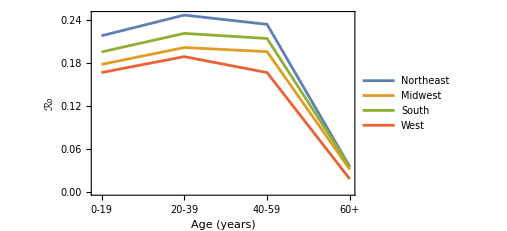

```mathematica
f11=ListPlot[Table[Tooltip[ l0[[i]],RN[[i]]],{i,1,m}],PlotMarkers->None,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Age (years)","ℛ_0"},FrameTicks->{{Automatic,Automatic},{dTcks,None}},PlotLegends->RN,LabelStyle->Directive[FontSize->12,FontFamily->"Arial"],ImageSize->375]
```

## Method by Ludmil and Yuliya

```mathematica
OptimalChi1={{3.004578161051320220*^-3,6.063747923999046954*^-3,3.545425576831823678*^-3,2.236626067229857952*^-14},
{4.398722516730560125*^-3,4.449697286182037123*^-3,5.958627241133407706*^-3,6.642807744610886198*^-11},
{3.537310173540902242*^-3,4.151002856664137187*^-3,3.181218010565318565*^-3,2.718994501058789159*^-14},
{6.054774009199111705*^-3,3.829806663471072622*^-3,4.735452868049963744*^-3,4.596756904901710390*^-11}}
```

{{0.00300457816105132022,0.00606374792399904695,0.00354542557683182368,2.23662606722985795×10^-14},{0.00439872251673056013,0.00444969728618203712,0.00595862724113340771,6.6428077446108862×10^-11},{0.00353731017354090224,0.00415100285666413719,0.00318121801056531857,2.71899450105878916×10^-14},{0.00605477400919911171,0.00382980666347107262,0.00473545286804996374,4.59675690490171039×10^-11}}

```mathematica
Total[Transpose[OptimalChi1*Sstar]](*check constraint *)
```

{146870.,227440.,306438.,267291.}

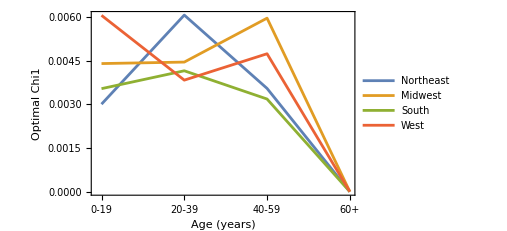

```mathematica
fXXC=ListPlot[Table[Tooltip[ OptimalChi1[[i]],RN[[i]]],{i,1,m}],PlotMarkers->None,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Age (years)","Optimal Chi1"},FrameTicks->{{Automatic,Automatic},{dTcks,None}},PlotLegends->RN,LabelStyle->Directive[FontSize->12,FontFamily->"Arial"],ImageSize->375]
```

### RN with the optimal Chi1--OptimalChi1

```mathematica
(*mχ1={{χ111,χ112,χ113,χ114},{χ121,χ122,χ123,χ124},{χ131,χ132,χ133,χ134},{χ141,χ142,χ143,χ144}}=OptimalChi1*)
mχ1={{χ111,χ112,χ113,χ114},{χ121,χ122,χ123,χ124},{χ131,χ132,χ133,χ134},{χ141,χ142,χ143,χ144}}=OptimalChi1 (*{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};*)
mχ2={{χ211,χ212,χ213,χ214},{χ221,χ222,χ223,χ224},{χ231,χ232,χ233,χ234},{χ241,χ242,χ243,χ244}}={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};(*{{0.002,0.007,0.0006,0.0003},{0.003,0.012,0.001,0.0007},{0.006,0.024,0.002,0.001},{0.015,0.054,0.005,0.003}};*)
mχ3={{χ311,χ312,χ313,χ314},{χ321,χ322,χ323,χ324},{χ331,χ332,χ333,χ334},{χ341,χ342,χ343,χ344}}={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
```

{{0.00300457816105132022,0.00606374792399904695,0.00354542557683182368,2.23662606722985795×10^-14},{0.00439872251673056013,0.00444969728618203712,0.00595862724113340771,6.6428077446108862×10^-11},{0.00353731017354090224,0.00415100285666413719,0.00318121801056531857,2.71899450105878916×10^-14},{0.00605477400919911171,0.00382980666347107262,0.00473545286804996374,4.59675690490171039×10^-11}}

```mathematica
sdfe=Table[mN[[i,j]]×(1+mχ1[[i,j]]/(ωv+ϵ2 mχ2⟦i,j⟧)(1+(ϵ2 mχ2⟦i,j⟧)/ω+(ϵ2 mχ2⟦i,j⟧)/ω×(1+(ϵ3 mχ3⟦i,j⟧)/ω)))^(-1),{i,1,m},{j,1,n}];
vdfe=Table[mχ1[[i,j]]/(ωv+ϵ2 mχ2⟦i,j⟧)×sdfe[[i,j]],{i,1,m},{j,1,n}];
pdfe=Table[(ϵ2 mχ2⟦i,j⟧)/ω×vdfe⟦i,j⟧,{i,1,m},{j,1,n}];
Y=Table[vψS[[j]]×vS[[i]]×ma[[i,j]]×vβ[[j]]×(sdfe[[i,j]]/mN[[i,j]]),{i,1,m},{j,1,n}];
Z=Table[vψS[[j]]×vS[[i]]×ma[[i,j]]×vβ[[j]]×((1-ϵ1)×vdfe[[i,j]]+pdfe[[i,j]])/mN[[i,j]],{i,1,m},{j,1,n}];
Table[Ωmat[[i]]=DiagonalMatrix[Flatten[Table[{Y[[i,j]],Z[[i,j]]},{j,1,n}]]],{i,1,m}];
Table[mH[[i,p]]=Dot[Ωmat[[i]],ccMat[[i,p]],ψImat[[p]],Q],{i,1,m},{p,1,m}];
L1=Partition[Flatten[Transpose[Table[mH[[1,p]],{p,1,m}]]],m×2n];
L2=Partition[Flatten[Transpose[Table[mH[[2,p]],{p,1,m}]]],m×2n];
L3=Partition[Flatten[Transpose[Table[mH[[3,p]],{p,1,m}]]],m×2n];
L4=Partition[Flatten[Transpose[Table[mH[[4,p]],{p,1,m}]]],m×2n];
NGMx=Join[L1,L2,L3,L4];
```

```mathematica
Eigenvalues[NGMx,1]
```

{4.7128}

```mathematica
Export["NGMx.csv",NGMx]
```

NGMx.csv

### RN with the Chi1 values following the pattern shown in Figure f11 above

```mathematica
l0={{0.22355562536934626,0.24791487446658117,0.23178889192271754,0.034510966529755153},{0.1815431132174088,0.20127892880934503,0.19137158756814973,0.028787888791755627},{0.19936130666301938,0.22105692608163208,0.20955038315149774,0.03228720752923144},{0.1685920236035752,0.18702861840401064,0.15976616670663327,0.015097661560599262}};
scale={0.01718580823153429,0.024499694107403585,0.016472195434267065,0.027251035887713583};
newChi1=scale*l0
```

{{0.00384198,0.00426062,0.00398348,0.000593099},{0.00444775,0.00493127,0.00468855,0.000705294},{0.00328392,0.00364129,0.00345175,0.000531841},{0.00459431,0.00509672,0.00435379,0.000411427}}

```mathematica
(*mχ1={{χ111,χ112,χ113,χ114},{χ121,χ122,χ123,χ124},{χ131,χ132,χ133,χ134},{χ141,χ142,χ143,χ144}}=OptimalChi1*)
mχ1={{χ111,χ112,χ113,χ114},{χ121,χ122,χ123,χ124},{χ131,χ132,χ133,χ134},{χ141,χ142,χ143,χ144}}=newChi1(*{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};*)
mχ2={{χ211,χ212,χ213,χ214},{χ221,χ222,χ223,χ224},{χ231,χ232,χ233,χ234},{χ241,χ242,χ243,χ244}}={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};(*{{0.002,0.007,0.0006,0.0003},{0.003,0.012,0.001,0.0007},{0.006,0.024,0.002,0.001},{0.015,0.054,0.005,0.003}};*)
mχ3={{χ311,χ312,χ313,χ314},{χ321,χ322,χ323,χ324},{χ331,χ332,χ333,χ334},{χ341,χ342,χ343,χ344}}={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
```

{{0.00384198,0.00426062,0.00398348,0.000593099},{0.00444775,0.00493127,0.00468855,0.000705294},{0.00328392,0.00364129,0.00345175,0.000531841},{0.00459431,0.00509672,0.00435379,0.000411427}}

### Checking constraint for Chi1

```mathematica
Sstar={{1.0600216151660305*^7,1.1947824997470027*^7,1.200765016794735*^7,1.2488303055892894*^7},{1.4987652030268373*^7,1.6016533803076502*^7,1.5145225873499423*^7,1.5295304221225757*^7},{2.714573794622607*^7,2.9291708309119027*^7,2.7921743967612088*^7,2.680293855830742*^7},{1.7516265188547775*^7,2.023022880905246*^7,1.768703243117786*^7,1.6290434385275263*^7}};
```

```mathematica
TotalDoses=Total[Transpose[{{279,62294,60028,24269},{898,92762,96407,37373},{1180,115330,133603,56325},{749,107797,119699,39046}}]]
```

{146870,227440,306438,267291}

```mathematica
Total[Transpose[newChi1*Sstar]]
```

{146870.,227440.,306438.,267291.}

### So, the constraint is satisfied.

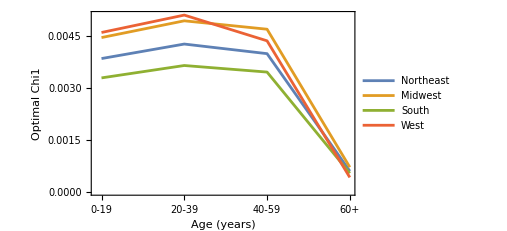

```mathematica
f11C=ListPlot[Table[Tooltip[ newChi1[[i]],RN[[i]]],{i,1,m}],PlotMarkers->None,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Age (years)","Optimal Chi1"},FrameTicks->{{Automatic,Automatic},{dTcks,None}},PlotLegends->RN,LabelStyle->Directive[FontSize->12,FontFamily->"Arial"],ImageSize->375]
```

```mathematica
newChi1
```

{{0.00384198,0.00426062,0.00398348,0.000593099},{0.00444775,0.00493127,0.00468855,0.000705294},{0.00328392,0.00364129,0.00345175,0.000531841},{0.00459431,0.00509672,0.00435379,0.000411427}}

```mathematica
{{0.0038419841066783065,0.00426061749032756,0.003983479446783651,0.0005930988526652704},{0.004447750741132252,0.004931272186094816,0.004688545356267867,0.0007052944693959651},{0.003283918405384104,0.003641292888514972,0.003451754864597015,0.0005318411924482393},{0.004594307285603283,0.005096723592157183,0.004353793542564894,0.00041142691700844433}};
```

```mathematica
mχ1
```

{{0.00384198,0.00426062,0.00398348,0.000593099},{0.00444775,0.00493127,0.00468855,0.000705294},{0.00328392,0.00364129,0.00345175,0.000531841},{0.00459431,0.00509672,0.00435379,0.000411427}}

```mathematica
mχ2
mχ3
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*mχ1=chi1*)
```

```mathematica
sdfe=Table[mN[[i,j]]×(1+mχ1[[i,j]]/(ωv+ϵ2 mχ2⟦i,j⟧)(1+(ϵ2 mχ2⟦i,j⟧)/ω+(ϵ2 mχ2⟦i,j⟧)/ω×(1+(ϵ3 mχ3⟦i,j⟧)/ω)))^(-1),{i,1,m},{j,1,n}];
vdfe=Table[mχ1[[i,j]]/(ωv+ϵ2 mχ2⟦i,j⟧)×sdfe[[i,j]],{i,1,m},{j,1,n}];
pdfe=Table[(ϵ2 mχ2⟦i,j⟧)/ω×vdfe⟦i,j⟧,{i,1,m},{j,1,n}];
Y=Table[vψS[[j]]×vS[[i]]×ma[[i,j]]×vβ[[j]]×(sdfe[[i,j]]/mN[[i,j]]),{i,1,m},{j,1,n}]
Z=Table[vψS[[j]]×vS[[i]]×ma[[i,j]]×vβ[[j]]×((1-ϵ1)×vdfe[[i,j]]+pdfe[[i,j]])/mN[[i,j]],{i,1,m},{j,1,n}]
Table[Ωmat[[i]]=DiagonalMatrix[Flatten[Table[{Y[[i,j]],Z[[i,j]]},{j,1,n}]]],{i,1,m}]//Quiet;
Table[mH[[i,p]]=Dot[Ωmat[[i]],ccMat[[i,p]],ψImat[[p]],Q],{i,1,m},{p,1,m}];
L1=Partition[Flatten[Transpose[Table[mH[[1,p]],{p,1,m}]]],m×2n];
L2=Partition[Flatten[Transpose[Table[mH[[2,p]],{p,1,m}]]],m×2n];
L3=Partition[Flatten[Transpose[Table[mH[[3,p]],{p,1,m}]]],m×2n];
L4=Partition[Flatten[Transpose[Table[mH[[4,p]],{p,1,m}]]],m×2n];
NGM=Join[L1,L2,L3,L4];
```

{{8.60217,7.89844,7.47815,5.40841},{8.1686,7.49014,7.08519,5.19458},{9.89283,9.09556,8.59436,6.14729},{7.3536,6.74015,6.45028,4.72788}}

{{0.172329,0.175472,0.155329,0.016726},{0.189445,0.192594,0.173214,0.0191036},{0.169398,0.172695,0.154685,0.0170475},{0.176163,0.179125,0.146434,0.0101427}}

```mathematica
Re[Eigenvalues[NGM,1]]
```

{4.72566}

```mathematica
f11B=ListPlot[Table[Tooltip[ newChi1[[i]],RN[[i]]],{i,1,m}],PlotMarkers->None,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Age (years)","Optimal Chi1"},FrameTicks->{{Automatic,Automatic},{dTcks,None}},PlotLegends->RN,LabelStyle->Directive[FontSize->12,FontFamily->"Arial"],ImageSize->375]
```

-Graphics-

```mathematica
Export["nMatrix.csv",mN];
Export["aMatrix.csv",ma];
Export["cMatrix.csv",mc];
Export["betaVector.csv",vβ];
(*Export["chi1Matrix.csv",mχ1];
Export["chi2Matrix.csv",mχ2];
Export["chi3Matrix.csv",mχ3];
Export["pnMatrix.csv",pdfe];
Export["snMatrix.csv",sdfe];
Export["vnMatrix.csv",vdfe];
Export["yMatrix.csv",Y];
Export["zMatrix.csv",Z];
Export["ccmMatrix.csv",ccM];
Export["ccmatMatrix.csv",ccMat];
Export["qMatrix.csv",Q];
Export["hMatrix.csv",mH];
*)
```